```mathematica
SetDirectory[NotebookDirectory[]];
Needs["PlotLegends`"]
```

# English Baselines

```mathematica
englishU={{" ",0.11965},{"u",0.0242803},{"e",0.111823},{"m",0.0211814},{"t",0.0797253},{"w",0.0207765},{"a",0.0718989},{"f",0.0196144},{"o",0.0660886},{"g",0.0177392},{"i",0.0613258},{"y",0.0173783},{"n",0.0594154},{"p",0.0169821},{"s",0.0557003},{"b",0.013135},{"h",0.0536491},{"v",0.00860991},{"r",0.0527071},{"k",0.00679637},{"d",0.0374417},{"j",0.00134695},{"l",0.0354345},{"x",0.00132054},{"c",0.0244916},{"q",0.000836341},{"z",0.000651466}};
```

```mathematica
englishD={{"e ",1000},{" t",879},{"th",858},{"he",710},{"d ",639},{" a",526},{"s ",475},{"t ",465},{"an",440},{"n ",385},{" s",360},{"nd",354},{"in",332},{" o",331},{" h",307},{"er",305},{" w",301},{"r ",271},{"y ",270},{"re",259},{"ha",249},{" i",244},{"f ",228},{" b",227},{"of",216},{"o ",215},{"or",208},{"at",204},{"en",200},{"ou",194},{"on",192},{" m",189},{"h ",187},{"hi",184},{" f",179},{"to",178},{"it",167},{"l ",166},{"es",166},{" c",166},{"is",164},{"al",158},{"ed",157},{"se",154},{"ar",146},{"ng",145},{"ve",142},{"ll",141},{"nt",139},{"st",134},{" d",129},{"as",128},{"me",127},{" l",125},{" p",124},{"be",121},{"ea",121},{"te",119},{"le",119},{"m ",118},{"g ",112},{" n",107},{"ne",107},{"ho",106},{" g",102},{"sh",98},{"fo",97},{"ti",92},{"ri",92},{" u",90},{" e",90},{"ro",89},{"no",87},{"de",87},{"un",86},{"ch",86},{"el",84},{"wi",84},{"wh",84},{"lo",82},{"om",81},{"et",80},{"co",80},{"ma",80},{"sa",78},{"il",77},{"ut",75},{"ai",75},{"ot",74},{"ee",74},{"us",73},{" r",73},{"ra",73},{"ur",72},{"wa",72},{"we",70},{"so",69},{"ce",68},{"rd",66},{"im",64},{"li",64},{"la",63},{"em",62},{" y",61},{"ic",61},{"ow",60},{"ca",60},{"pe",59},{"id",59},{"ay",56},{"ns",56},{"am",56},{"ld",56},{"ie",55},{"ad",54},{"io",52},{"ta",52},{"ir",51},{"mo",51},{"di",51},{"av",50},{"gh",50},{"ke",50},{"ey",49},{"rs",49},{"go",48},{"si",48},{"ec",48},{"ac",48},{"ly",47},{"ss",47},{"pr",45},{"od",45},{"rt",44},{"ul",44},{"ev",43},{"ei",43},{"ge",43},{"u ",42},{"w ",41},{"bu",41},{"tr",41},{"nc",41},{"os",39},{"wo",39},{"do",39},{"ol",39},{"ig",38},{"ts",37},{"po",37},{"oo",37},{" j",37},{"mi",37},{"ab",37},{"k ",36},{"ht",36},{" k",36},{"fe",36},{"if",35},{"ye",35},{"da",35},{"iv",34},{"yo",34},{"na",34},{"up",33},{"pl",33},{"fi",33},{"pa",32},{"ct",31},{"fr",31},{"ni",31},{"sp",30},{"ga",30},{"su",29},{"vi",29},{"ry",28},{"br",28},{"bo",28},{"ak",28},{"fa",28},{"p ",27},{"rn",27},{"ki",27},{"bl",26},{"ef",26},{"my",25},{"op",25},{"ci",25},{"hy",24},{"by",24},{"ov",24},{" v",24},{"gr",24},{"ep",24},{"ag",24},{"ty",23},{"ds",23},{"tu",22},{"tt",22},{"ug",22},{"ff",22},{"ia",22},{"ru",21},{"eo",21},{"ls",20},{"gi",20},{"ah",20},{"au",19},{"lt",19},{"dr",19},{"ck",19},{"uc",19},{"ba",19},{"ap",18},{"va",18},{"a ",17},{"hr",17},{"ny",16},{"hu",16},{"ft",16},{"wn",16},{"je",16},{"ex",15},{"ew",15},{"mp",15},{"rm",15},{"cl",15},{"ok",15},{"ph",15},{"aw",14},{"cu",14},{"gs",14},{"cr",14},{"tl",14},{"pi",14},{"bi",14},{"eg",14},{"ud",14},{"tw",13},{"mu",13},{"pt",13},{"ys",13},{"pp",13},{"kn",13},{"oi",13},{"af",13},{"ae",13},{"rr",12},{"sc",12},{"mb",12},{"rv",11},{"qu",11},{"pu",11},{"ju",11},{"fu",11},{"du",11},{"ms",11},{"um",11},{"mm",11},{"fl",11},{"rk",11},{"ui",11},{"eh",11},{"oc",11},{"sr",10},{"jo",10},{"ue",10},{"cc",10},{"ub",10},{"ob",10},{"ua",10},{"oa",10},{"ip",9},{"nn",9},{"sl",9},{"rl",9},{"yi",9},{"rg",9},{"lf",9},{"rc",9},{"sw",8},{"nu",8},{"gl",8},{"nk",8},{"ik",8},{"og",8},{"b ",7},{"lv",7},{"lu",7},{"vo",7},{"ib",7},{"dy",6},{"gu",6},{"ks",6},{"dn",6},{"sm",6},{"nl",6},{"dg",6},{"oe",6},{"eb",6},{"i ",5},{"c ",5},{"xt",5},{"ps",5},{"bs",5},{"wr",5},{"dl",5},{"ze",5},{"ja",5},{"aa",5},{" z",4},{"sy",4},{"oy",4},{"ws",4},{" q",4},{"yp",4},{"rp",4},{"gn",4},{"sk",4},{"lk",4},{"ek",4},{"nh",4},{"rf",4},{"nf",4},{"dd",4},{"tc",4},{"x ",3},{"az",3},{"gy",3},{"cy",3},{"ix",3},{"dw",3},{"mr",3},{"eq",3},{"xp",3},{"sn",3},{"dm",3},{"wl",3},{"zi",3},{"oh",3},{"gg",3},{"za",3},{"iz",2},{"ez",2},{"lw",2},{"nv",2},{"dv",2},{"eu",2},{"gt",2},{"bt",2},{"hs",2},{"yr",2},{"lp",2},{"ko",2},{"ao",2},{"tn",2},{"lm",2},{"gm",2},{"yl",2},{"xi",2},{"ji",2},{"uf",2},{"xe",2},{"gd",2},{"xc",2},{"yb",2},{"rb",2},{"bb",2},{"xa",2},{"z ",1},{"v ",1},{"zz",1},{"uz",1},{"oz",1},{"wy",1},{"py",1},{"fy",1},{"ox",1},{"ax",1},{"rw",1},{"nw",1},{"iu",1},{"yt",1},{"fs",1},{"zr",1},{"lr",1},{"sq",1},{"nq",1},{"iq",1},{"cq",1},{"zo",1},{"uo",1},{"yn",1},{"mn",1},{"hn",1},{"bn",1},{"ym",1},{"tm",1},{"hm",1},{"kl",1},{"hl",1},{"uk",1},{"oj",1},{"nj",1},{"ij",1},{"ej",1},{"bj",1},{"rh",1},{"sg",1},{"tf",1},{"sf",1},{"mf",1},{"hf",1},{"df",1},{"sd",1},{"mc",1},{"lc",1},{"sb",1},{"nb",1},{"hb",1},{"ya",1},{"ka",1}};
englishD=Transpose[englishD]{1,(1/(Transpose[englishD][[2]]//Total))}//N//Transpose//Sort;
```

```mathematica
englishDAll=Tuples[Join[{" "},CharacterRange["a","z"]],2];
englishDAll=Reap[For[i=1,i≤Length[englishDAll],i++,
Sow[englishDAll[[i]][[1]]<>englishDAll[[i]][[2]]]
]][[2]][[1]];
```

```mathematica
missingEnglishD=Complement[englishDAll,Transpose[englishD][[1]]];
englishD=If[missingEnglishD≠{},Join[englishD,{missingEnglishD,Table[0,{Length[missingEnglishD]}]}//Transpose],englishD];
```

# Unigrams

```mathematica
textUSE=Import["unigram-small-efficient.txt"];
Length[Characters[textUSE]]
textUBE=Import["unigram-big-efficient.txt"];
Length[Characters[textUBE]]
textUSA=Import["unigram-small-accurate.txt"];
Length[Characters[textUSA]]
textUBA=Import["unigram-big-accurate.txt"];
Length[Characters[textUBA]]
```

498

256946

617

332774

```mathematica
spdf=Characters[textUSE]//Tally;
smallUE=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=Characters[textUBE]//Tally;
bigUE=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=Characters[textUSA]//Tally;
smallUA=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=Characters[textUBA]//Tally;
bigUA=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
```

```mathematica
smallUE//Length
bigUE//Length
smallUA//Length
bigUA//Length
```

27

27

27

«1 more identical outputs»

```mathematica
missingUE=Complement[Transpose[bigUE][[1]],Transpose[smallUE][[1]]]
smallUE=If[missingUE≠{},Join[smallUE,{missingUE,Table[0,{Length[missingUE]}]}//Transpose],smallUE];
missingUA=Complement[Transpose[bigUA][[1]],Transpose[smallUA][[1]]]
smallUA=If[missingUA≠{},Join[smallUA,{missingUA,Table[0,{Length[missingUA]}]}//Transpose],smallUA];
```

{}

{}

# Digrams

```mathematica
GetDigrams[s0_]:=Module[{s=s0,chars,i},
chars=Characters[s];
Reap[For[i=1,i<Length[chars],i++,
Sow[chars[[i]]<>chars[[i+1]]]
]][[2]][[1]]
]
```

```mathematica
textDSE=Import["digram-small-efficient.txt"];
Length[Characters[textDSE]]
textDBE=Import["digram-big-efficient.txt"];
Length[Characters[textDBE]]
textDSA=Import["digram-small-accurate.txt"];
Length[Characters[textDSA]]
textDBA=Import["digram-big-accurate.txt"];
Length[Characters[textDBA]]
```

558

270396

528

355834

```mathematica
spdf=GetDigrams[textDSE]//Tally;
smallDE=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=GetDigrams[textDBE]//Tally;
bigDE=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=GetDigrams[textDSA]//Tally;
smallDA=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
spdf=GetDigrams[textDBA]//Tally;
bigDA=Transpose[spdf]{1,(1/(Transpose[spdf][[2]]//Total))}//N//Transpose//Sort;
```

```mathematica
smallDE//Length
bigDE//Length
smallDA//Length
bigDA//Length
```

729

729

729

«1 more identical outputs»

```mathematica
missingDE=Complement[englishDAll,Transpose[smallDE][[1]]]
smallDE=If[missingDE≠{},Join[smallDE,{missingDE,Table[0,{Length[missingDE]}]}//Transpose],smallDE];
missingDA=Complement[englishDAll,Transpose[smallDA][[1]]]
smallDA=If[missingDA≠{},Join[smallDA,{missingDA,Table[0,{Length[missingDA]}]}//Transpose],smallDA];
missingDE=Complement[englishDAll,Transpose[bigDE][[1]]]
bigDE=If[missingDE≠{},Join[bigDE,{missingDE,Table[0,{Length[missingDE]}]}//Transpose],bigDE];
missingDA=Complement[englishDAll,Transpose[bigDA][[1]]]
bigDA=If[missingDA≠{},Join[bigDA,{missingDA,Table[0,{Length[missingDA]}]}//Transpose],bigDA];
```

{}

{}

{}

«1 more identical outputs»

# Unigram Processing

```mathematica
ListPlot[{(Transpose[Sort[smallUE]][[2]]-Transpose[Sort[englishU]][[2]])/(Transpose[Sort[englishU]][[2]]),
(Transpose[Sort[bigUE]][[2]]-Transpose[Sort[englishU]][[2]])/(Transpose[Sort[englishU]][[2]]),
(Transpose[Sort[smallUA]][[2]]-Transpose[Sort[englishU]][[2]])/(Transpose[Sort[englishU]][[2]]),
(Transpose[Sort[bigUA]][[2]]-Transpose[Sort[englishU]][[2]])/(Transpose[Sort[englishU]][[2]])},Joined->True,PlotRange->All,PlotLegend->{"Small, efficient","Large, efficient","Small, accurate","Large, accurate"},PlotStyle->{Thick}]
```

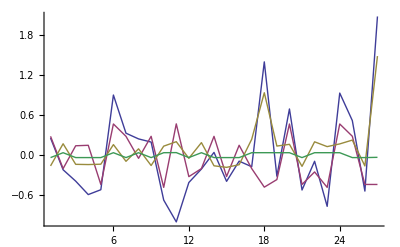

```mathematica
ListPlot[{Transpose[smallUA][[2]]//Sort, Transpose[bigUA][[2]]//Sort, Transpose[englishU][[2]]//Sort},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick}]
ListPlot[{Transpose[Sort[smallUA]][[2]], Transpose[Sort[bigUA]][[2]], Transpose[Sort[englishU]][[2]]},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick}]
```

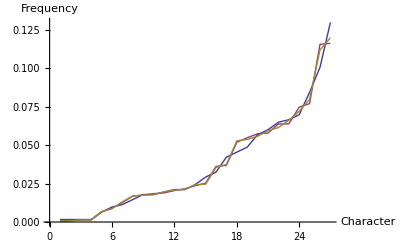

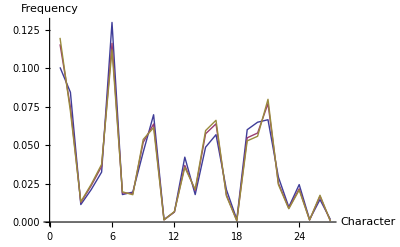

```mathematica
ListPlot[{Transpose[smallUE][[2]]//Sort, Transpose[bigUE][[2]]//Sort, Transpose[englishU][[2]]//Sort},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick}]
ListPlot[{Transpose[Sort[smallUE]][[2]], Transpose[Sort[bigUE]][[2]], Transpose[Sort[englishU]][[2]]},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick},PlotRange->All]
```

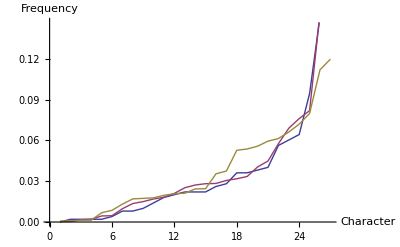

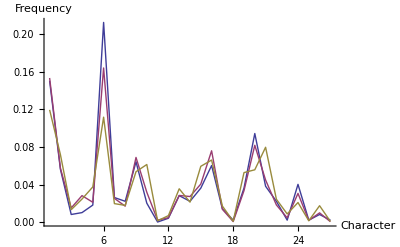

```mathematica
ListPlot[{Transpose[smallUA][[2]]//Sort, Transpose[smallUE][[2]]//Sort, Transpose[englishU][[2]]//Sort},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick}]
ListPlot[{Transpose[Sort[smallUA]][[2]], Transpose[Sort[smallUE]][[2]], Transpose[Sort[englishU]][[2]]},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick},PlotRange->All]
```

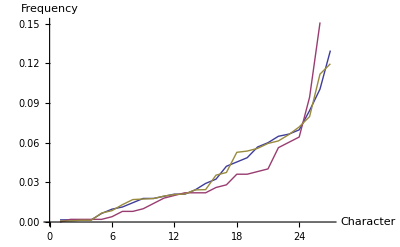

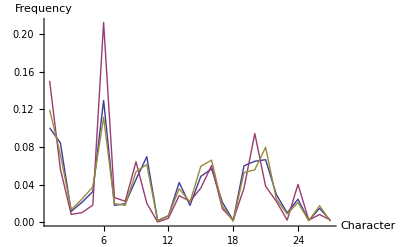

```mathematica
ListPlot[{Transpose[bigUA][[2]]//Sort, Transpose[bigUE][[2]]//Sort, Transpose[englishU][[2]]//Sort},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick}]
ListPlot[{Transpose[Sort[bigUA]][[2]], Transpose[Sort[bigUE]][[2]], Transpose[Sort[englishU]][[2]]},Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick}]
```

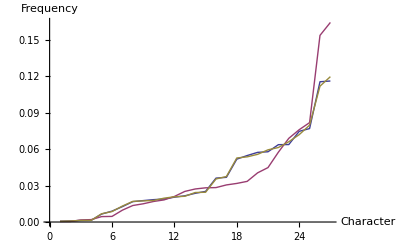

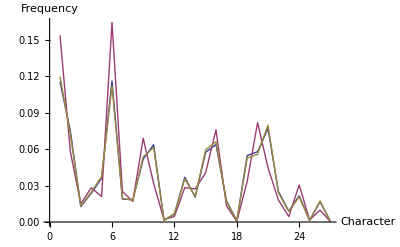

# Digram Processing

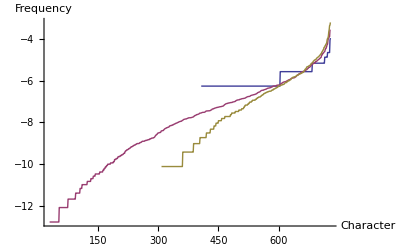

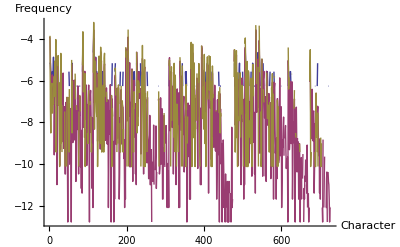

```mathematica
ListPlot[Log[{Transpose[smallDA][[2]]//Sort, Transpose[bigDA][[2]]//Sort, Transpose[englishD][[2]]//Sort}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick},PlotRange->All]
ListPlot[Log[{Transpose[Sort[smallDA]][[2]], Transpose[Sort[bigDA]][[2]], Transpose[Sort[englishD]][[2]]}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick},PlotRange->All]
```

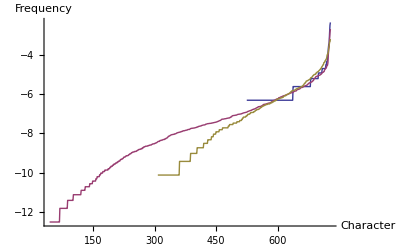

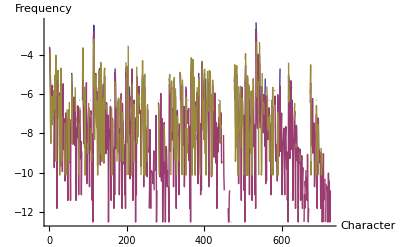

```mathematica
ListPlot[Log[{Transpose[smallDE][[2]]//Sort, Transpose[bigDE][[2]]//Sort, Transpose[englishD][[2]]//Sort}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick},PlotRange->All]
ListPlot[Log[{Transpose[Sort[smallDE]][[2]], Transpose[Sort[bigDE]][[2]], Transpose[Sort[englishD]][[2]]}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Small sample","Large sample","English"},PlotStyle->{Thick},PlotRange->All]
```

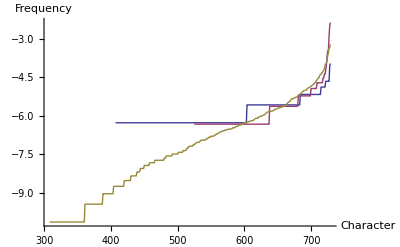

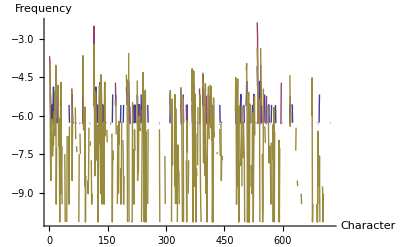

```mathematica
ListPlot[Log[{Transpose[smallDA][[2]]//Sort, Transpose[smallDE][[2]]//Sort, Transpose[englishD][[2]]//Sort}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick},PlotRange->All]
ListPlot[Log[{Transpose[Sort[smallDA]][[2]], Transpose[Sort[smallDE]][[2]], Transpose[Sort[englishD]][[2]]}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick},PlotRange->All]
```

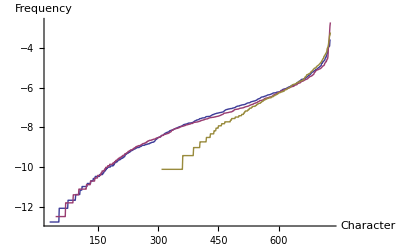

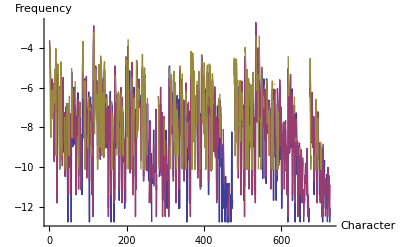

```mathematica
ListPlot[Log[{Transpose[bigDA][[2]]//Sort, Transpose[bigDE][[2]]//Sort, Transpose[englishD][[2]]//Sort}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick},PlotRange->All]
ListPlot[Log[{Transpose[Sort[bigDA]][[2]], Transpose[Sort[bigDE]][[2]], Transpose[Sort[englishD]][[2]]}],Joined->True,ImageSize->400,AxesLabel->{"Character","Frequency"},PlotLegend->{"Accurate","Efficient","English"},PlotStyle->{Thick},PlotRange->All]
```